## Problema 1

El jugador de basquetbol  lanza la pelota al suelo desde una altura de 1 m, con una velocidad de v0 (m/s) y un ángulo de -50° con respecto a la horizontal.  ¿Cuál es el valor de v0 para que la pelota enceste  en el aro rebotando inelasticamente en el suelo, solo perdiendo en el rebote  un 5% de su energía cinética total? (la figura tiene datos de referencia).

// Se definen los datos iniciales

```mathematica
g=9.81;
θ=-50 Degree;
```

```mathematica
ecs={y''[t]==-g,x''[t]==0} (*La aceleracion en el eje y es -g, y el eje x no posee aceleracion*)
```

{y''[t]==-9.81,x''[t]==0}

```mathematica
Clear[condini] (*Comando para limmpiar condiciones iniciales en caso de error*)
```

// Definimos una funcion, llamada condicion inicial, la cual al ingresar la velocidad inicial, nos entrega los datos iniciales en forma de ecuaciones;
* La posicion inicial, un metro de altura y[0] = 1 y definimos el origen en los pies del player x[0] = 0
* Las velocidades iniciales: (aqui es donde entra el comportamiento de funcion, con ingresar la velocidad inicial entrega sus debidos componentes, recordemos que el angulo de lanzamiento lo definimos al comienzo)
	Vy[0] = y’[0] = Vo * Sin[angulo de lanzamiento]
	Vx[0] = x’[0] = Vo * Cos[angulo de lanzamiento]

```mathematica
condini[v0_]={y[0]==1,x[0]==0,y'[0]== v0 Sin[θ],x'[0]==v0 Cos[θ]}
```

{y[0]==1,x[0]==0,y'[0]==-v0 Cos[40 °],x'[0]==v0 Sin[40 °]}

//Definimos la funcion Solucion, la cual nos entrega una solucion a la ecuacion diferencial (observable en un parametic plot) a una determinada velocidad inicial

```mathematica
sol[v0_]:=First@NDSolve[Join[ecs,condini[v0]],{x,y},{t,0,3}]
```

```mathematica
solutest=sol[10] (*Probamos una solucion cualquiera*)
```

{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}

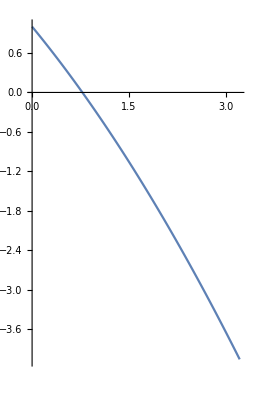

```mathematica
ParametricPlot[{x[t]/.solutest,y[t]/.solutest},{t,0,.5}] (*Notece que atraviesa el "suelo", lo arreglaremos con un WhenEvent ahora mismo*)
```

// Definimos una lista de ecuaciones para los eventos, para esto se utiliza un WhenEvent

```mathematica
eventos={WhenEvent[y[t]==0,y'[t]->-Sqrt[0.95]y'[t]],WhenEvent[x[t]==10,Tend=t;"StopIntegration"]};
```

La parte y’[t] -> - Sqrt[0.95] y’[t], indica que la velocidad en y disminuyo (de tal forma que contara por una perdida de un 5% de energia cinetica como dice el problema propuesto)
La parte Tend = t; quiere decir que cuando la posicion de x sea igual a 10 (x[t] == 10), definamos Tend (tiempo end) = al tiempo en que x[t]==10, y la siguiente parte ‘StopIntegration’ le indicamos que ya debe dejar de calcular luego de este momento

```mathematica
Join[ecs,condini[v0],eventos] (*Combinamos las ecuaciones necesarias para resolver esto, las cuales son:
ecs: en donde indicamos el valor de las segundas derivadas (aceleraciones)
conini: donde definimos los valores iniciales de posicion y los componentes de la velocidad inicial
eventos: las cosas que debe hacer luego de que se cumplan ciertos parametros, como el de alcanzar el piso, y luego rebotar con Sqrt[0.95] de la velocidad con que venia bajando *)
```

{y''[t]==-9.81,x''[t]==0,y[0]==1,x[0]==0,y'[0]==-v0 Cos[40 °],x'[0]==v0 Sin[40 °],WhenEvent[y[t]==0,y'[t]→-√0.95 y'[t]],WhenEvent[x[t]==10,Tend=t;StopIntegration]}

```mathematica
sol2[v0_]:=First@NDSolve[Join[ecs,condini[v0],eventos],{x,y},{t,0,3}]  (*Funcion de solucion con un cierta velocidad, esta teniendo en cuenta los eventos*)
```

```mathematica
solutest=sol2[10] (*Test de la solucion dos con 10 m/s como velocidad inicial para probar*)
```

{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}

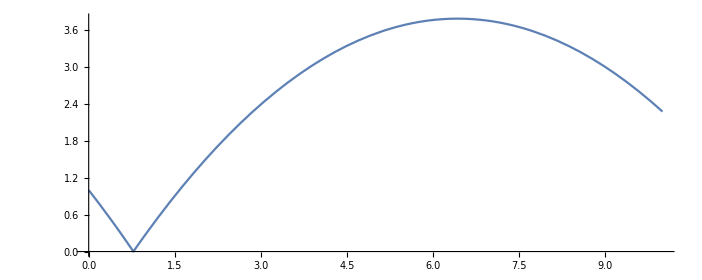

```mathematica
ParametricPlot[{x[t]/.solutest,y[t]/.solutest},{t,0,Tend}]
```

```mathematica
y[Tend]/.sol2[10.48] (*Observamos la altura a la que termina; segun el problema debe terminar a 3.05 m para encestar*)
```

3.33593

```mathematica
Clear[yfinal] (*Seccion de codigo usada para limpiar el valor yfinal en caso de errores*)
```

// Definimos la funcion y final para que difrectamente nos entregue la altura final en base a una velocidad inicial, basicamente comprimimos todo el codigo hecho hasta ahora

```mathematica
yfinal[v0_]:=Module[{},
Clear[Tend]; (*Resetea Tend, time end para que se resetee cada vez que corramos el codigo*)
solu=First@NDSolve[Join[ecs,{y[0]==1,x[0]==0,y'[0]== v0 Sin[θ],x'[0]==v0 Cos[θ]},eventos],{x,y},{t,0,3}];
tfin=Tend; (*Luego definimos tfin, ya que dentro de este codigo saldra Tend*)
(y[tfin]/.solu) (*Corre la ultima parte, entregando la altura de y, en el tiempo final, usando la solucion de la ecuacion diferencial*)]
```

//Graciamos el valor de la altura final, para hallar una aproximacion a nuestro valor buscado

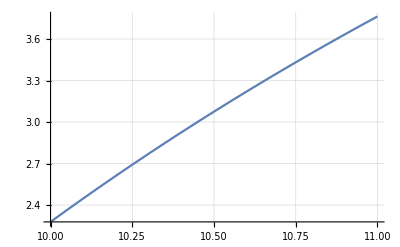

```mathematica
Plot[yfinal[v0],{v0,10.,11},GridLines->Automatic]
```

Asi nos acercamos a que la velocidad necesaria es 10.48301

```mathematica
yfinal[10.48301]
```

3.05

//Pero fue medio trucha eso de arriba, aqui una funcion para encontrar valores de n (velocidad inicial) de tal forma que el error sea pequeno (Como se media el error? xd)

```mathematica
Table[If[(yfinal[n]-3.05)^2<0.000001,n,##&[]],{n,10.,11,0.001}]
```

{10.483}

## θ = -35

```mathematica
g=9.81;
θ=-35 Degree;
```

```mathematica
ecs={y''[t]==-g,x''[t]==0}
```

{y''[t]==-9.81,x''[t]==0}

```mathematica
Clear[condini]
```

```mathematica
condini[v0_]={y[0]==1,x[0]==0,y'[0]== v0 Sin[θ],x'[0]==v0 Cos[θ]}
```

{y[0]==1,x[0]==0,y'[0]==-v0 Sin[35 °],x'[0]==v0 Cos[35 °]}

```mathematica
eventos={WhenEvent[y[t]==0,y'[t]->-Sqrt[0.95]y'[t]],WhenEvent[x[t]==10,Tend=t;"StopIntegration"]};
```

```mathematica
Clear[sol2]
```

```mathematica
Join[ecs,condini[v0],eventos]
```

{y''[t]==-9.81,x''[t]==0,y[0]==1,x[0]==0,y'[0]==-v0 Sin[35 °],x'[0]==v0 Cos[35 °],WhenEvent[y[t]==0,y'[t]→-√0.95 y'[t]],WhenEvent[x[t]==10,Tend=t;StopIntegration]}

```mathematica
sol2[v0_]:=First@NDSolve[Join[ecs,condini[v0],eventos],{x,y},{t,0,3}]
```

```mathematica
solutest=sol2[10]
```

{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}

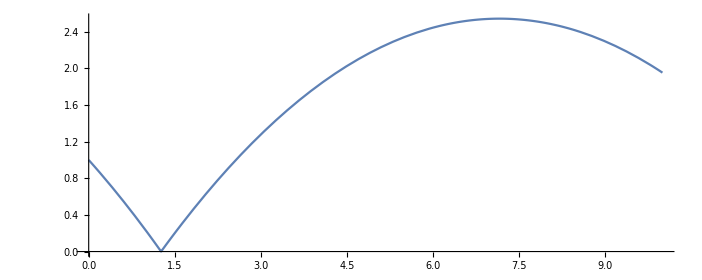

```mathematica
ParametricPlot[{x[t]/.solutest,y[t]/.solutest},{t,0,Tend}]
```

```mathematica
y[Tend]/.sol2[13.48]
```

InterpolatingFunction::dmval: Input value {1.04732} lies outside the range of data in the interpolating function. Extrapolation will be used.

3.83601

```mathematica
Clear[yfinal]
```

```mathematica
yfinal[v0_]:=Module[{},
Clear[Tend];
solu=First@NDSolve[Join[ecs,{y[0]==1,x[0]==0,y'[0]== v0 Sin[θ],x'[0]==v0 Cos[θ]},eventos],{x,y},{t,0,3}];
tfin=Tend;
(y[tfin]/.solu)]
```

```mathematica
yfinal[11.6567]
```

3.05028

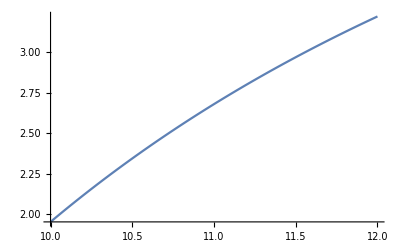

```mathematica
Plot[yfinal[v0],{v0,10.,12}]
```

```mathematica
yfit=Interpolation[Table[{v0,yfinal[v0]},{v0,10.,12,.001}]];
```

```mathematica
vsol=v0/.FindRoot[yfit[v0]==3.05,{v0,11.}]
```

11.6562

```mathematica
yfinal[vsol]
```

3.05